```mathematica
ff[n_,s_]:=s n^s HarmonicNumber[n,s]-(1-s)n^(1-s)HarmonicNumber[n,1-s]
```

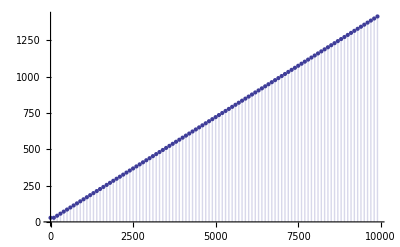

```mathematica
DiscretePlot[ Im@ff[n,N@ZetaZero@1],{n,1,10000,100}]
```

```mathematica
10000^(.5)
```

100.

```mathematica
N@Im@ZetaZero@1 (1000000)/100
```

141347.

```mathematica
ff[10000000, N@ZetaZero@1]-N@Im@ZetaZero@1 (10000000)/100I
```

0.-271.716 ⅈ

```mathematica
N[(Im@ZetaZero@1)^2]
```

199.79

```mathematica
Gamma[s/2]/.s->10
```

24

```mathematica
(s/2-1)!/.s->10
```

24

```mathematica
FullSimplify[(1-s)/2-1]
```

1/2 (-1-s)

```mathematica
4! 5
```

120

```mathematica
FullSimplify[(1/Zeta[s](n^s/s HarmonicNumber[n,s]+n^(1-s)/(1-s)HarmonicNumber[n,1-s])-n^s/s)/(-Pi^(1/2-s)n^(1-s)/(1-s))]
```

(π^(-1/2+s) (-n s HarmonicNumber[n,1-s]-n^(2 s) (-1+s) HurwitzZeta[s,1+n]))/(n s Zeta[s])

```mathematica
(π^(-1/2+s) (- s HarmonicNumber[n,1-s]-n^(2 s-1) (-1+s) HurwitzZeta[s,1+n]))/(s Zeta[s])
```

(π^(-1/2+s) (-s HarmonicNumber[n,1-s]-n^(-1+2 s) (-1+s) HurwitzZeta[s,1+n]))/(s Zeta[s])

```mathematica
Limit[(π^(-1/2+s) (-s HarmonicNumber[n,1-s]-n^(-1+2 s) (-1+s) HurwitzZeta[s,1+n]))/(s Zeta[s]),n->Infinity]
```

Limit[(π^(-1/2+s) (-s HarmonicNumber[n,1-s]-n^(-1+2 s) (-1+s) HurwitzZeta[s,1+n]))/(s Zeta[s]),n→∞]

```mathematica
(π^(-1/2+s) (-s n^-s HarmonicNumber[n,1-s]-n^(-1+ s) (-1+s) HurwitzZeta[s,1+n]))/(s n^-s Zeta[s])/.s->.5+3I/.n->10000000000
```

65613.9-102979. ⅈ

```mathematica
zetr[n_,s_]:=(n^s s  HarmonicNumber[n,s]+n^(1-s) (1-s) HarmonicNumber[n,1-s])/(n^s/s -Pi^(1/2-s) Gamma[s/2]/Gamma[(1-s)/2] n^(1-s)/(1-s))
```

```mathematica
Zeta[.51+5.5I]
```

0.764717+0.289062 ⅈ

```mathematica
al4[s_]:=-1/((1/2)Pi^(-s/2)Gamma[s/2])
ssosub3[n_,s_]:=(s^-1 n^s)/(al4[s]s^-1 n^s-al4[1-s](1-s)^-1 n^(1-s))HarmonicNumber[n,s]
sso10cc[n_,s_]:=ssosub3[n,s]+ssosub3[n,1-s]
szet10cc[n_,s_]:=al4[s] sso10cc[n,s] 
ssosub3dd[n_,s_]:=(s^-1 n^s)/(al4[s]s^-1 n^s-al4[1-s](1-s)^-1 n^(1-s))HarmonicNumber[n,s]
szet10dd[n_,s_]:=al4[s]  (((s^-1 n^s)/(al4[s]s^-1 n^s-al4[1-s](1-s)^-1 n^(1-s))HarmonicNumber[n,s])+(((1-s)^-1 n^(1-s))/(al4[(1-s)](1-s)^-1 n^(1-s)-al4[1-(1-s)](1-(1-s))^-1 n^(1-(1-s)))HarmonicNumber[n,(1-s)]))
szet10ee[n_,s_]:= (((s^-1 n^s)/(s^-1 n^s-al4[1-s]/al4[s](1-s)^-1 n^(1-s))HarmonicNumber[n,s])-(((1-s)^-1 n^(1-s))/(s^-1 n^(s)-al4[(1-s)]/al4[s](1-s)^-1 n^(1-s))HarmonicNumber[n,(1-s)]))
szet10ff[n_,s_]:= (((s^-1 n^s HarmonicNumber[n,s])/(s^-1 n^s-al4[1-s]/al4[s](1-s)^-1 n^(1-s)))-(((1-s)^-1 n^(1-s) HarmonicNumber[n,(1-s)])/(s^-1 n^(s)-al4[(1-s)]/al4[s](1-s)^-1 n^(1-s))))
zet10gg[n_,s_]:=(n^s HarmonicNumber[n,s]/s-n^(1-s) HarmonicNumber[n,(1-s)]/(1-s))/(n^s/s-al4[1-s]/al4[s] n^(1-s)/(1-s))
zet10hh[n_,s_]:=(n^s HarmonicNumber[n,s]/s-n^(1-s) HarmonicNumber[n,(1-s)]/(1-s))/(n^s/s-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2]n^(1-s)/(1-s))
```

```mathematica
zet10hh[100000,.51+5.5I]
```

0.767294+0.2896 ⅈ

```mathematica
g1a[n_,s_]:=(n^s HarmonicNumber[n,s]/s-n^(1-s) HarmonicNumber[n,(1-s)]/(1-s))/(n^s/s-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2]n^(1-s)/(1-s))
g1b[n_,s_]:=Zeta[s]
g2a[n_,s_]:=(n^s HarmonicNumber[n,s]/s-n^(1-s) HarmonicNumber[n,(1-s)]/(1-s))/Zeta[s]
g2b[n_,s_]:=(n^s/s-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2]n^(1-s)/(1-s))
g3a[n_,s_]:=((n^s HarmonicNumber[n,s]/s-n^(1-s) HarmonicNumber[n,(1-s)]/(1-s))/Zeta[s]-n^s/s)/(-Pi^(1/2-s)n^(1-s)/(1-s))
g3b[n_,s_]:=Gamma[s/2]/Gamma[(1-s)/2]
g4a[n_,s_]:=(π^(-1/2+s) (HarmonicNumber[n,1-s]-n^(2 s-1) (-1+s)/s HurwitzZeta[s,1+n]))/Zeta[s]
g4b[n_,s_]:=Gamma[s/2]/Gamma[(1-s)/2]
g5a[n_,s_]:=(π^(-1/2+s) HarmonicNumber[n,1-s])/Zeta[s]-π^(-1/2+s) n^(2 s-1) (-1+s)/s HurwitzZeta[s,1+n]/Zeta[s]
g5b[n_,s_]:=Gamma[s/2]/Gamma[(1-s)/2]
g6a[n_,s_]:=(π^(-1/2+s) Zeta[1-s])/Zeta[s]-(π^(-1/2+s) Zeta[1-s,n+1])/Zeta[s]-π^(-1/2+s) n^(2 s-1) (-1+s)/s Zeta[s,1+n]/Zeta[s]
g6b[n_,s_]:=Gamma[s/2]/Gamma[(1-s)/2]
g7a[n_,s_]:=π^(-1/2+s) Zeta[1-s]/Zeta[s]
g7b[n_,s_]:=Gamma[s/2]/Gamma[(1-s)/2]
```

```mathematica
{g7a[n,s],g7b[n,s]}/.n->1000000/.s->.3+4I
```

{-0.368269-0.789246 ⅈ,-0.368269-0.789246 ⅈ}

```mathematica
FullSimplify[((n^s HarmonicNumber[n,s]/s-n^(1-s) HarmonicNumber[n,(1-s)]/(1-s))/Zeta[s]-n^s/s)/(-Pi^(1/2-s)n^(1-s)/(1-s))]
```

(π^(-1/2+s) (n s HarmonicNumber[n,1-s]-n^(2 s) (-1+s) HurwitzZeta[s,1+n]))/(n s Zeta[s])

```mathematica
Zeta[.3]-Zeta[.3,1+10]
```

6.5046

```mathematica
HarmonicNumber[10,.3]
```

6.5046

```mathematica
g6ar[n_,s_]:={(π^(-1/2+s) Zeta[1-s])/Zeta[s],-(π^(-1/2+s) Zeta[1-s,n+1])/Zeta[s]-π^(-1/2+s) n^(2 s-1) (-1+s)/s Zeta[s,1+n]/Zeta[s]}
```

```mathematica
Chop@g6ar[n,s]/.n->100000000000000/.s->.3+4I
```

{-0.368269-0.789246 ⅈ,3.00133×10^-11+2.7012×10^-10 ⅈ}

```mathematica
h1a[n_,s_]:=(n^s HarmonicNumber[n,s]/s-n^(1-s) HarmonicNumber[n,(1-s)]/(1-s))/(n^s/s-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2]n^(1-s)/(1-s))
h1b[n_,s_]:=n^s HarmonicNumber[n,s]/s/(n^s/s-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2]n^(1-s)/(1-s))-n^(1-s) HarmonicNumber[n,(1-s)]/(1-s)/(n^s/s-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2]n^(1-s)/(1-s))
h1c[n_,s_]:=n^s (Zeta[s]-Zeta[s,n+1])/s/(n^s/s-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2]n^(1-s)/(1-s))-n^(1-s) (Zeta[1-s]-Zeta[1-s,n+1])/(1-s)/(n^s/s-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2]n^(1-s)/(1-s))
h1d[n_,s_]:=n^s (Zeta[s])/s/(n^s/s-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2]n^(1-s)/(1-s))-
n^s (Zeta[s,n+1])/s/(n^s/s-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2]n^(1-s)/(1-s))-
n^(1-s) (Zeta[1-s])/(1-s)/(n^s/s-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2]n^(1-s)/(1-s))+
n^(1-s) (Zeta[1-s,n+1])/(1-s)/(n^s/s-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2]n^(1-s)/(1-s))
h1dx[n_,s_]:={n^s (Zeta[s])/s/(n^s/s-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2]n^(1-s)/(1-s)),-
n^s (Zeta[s,n+1])/s/(n^s/s-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2]n^(1-s)/(1-s)),-
n^(1-s) (Zeta[1-s])/(1-s)/(n^s/s-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2]n^(1-s)/(1-s)),
n^(1-s) (Zeta[1-s,n+1])/(1-s)/(n^s/s-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2]n^(1-s)/(1-s))}
```

```mathematica
h1dx[1000000000000000000,.6+30I]
```

{0.0224625-0.566477 ⅈ,-324573.+416745. ⅈ,-0.000163445-0.0000318504 ⅈ,324573.-416745. ⅈ}

```mathematica
Zeta[.6+30I]
```

0.0222991-0.566509 ⅈ

```mathematica
n^s Zeta[s]/s/(n^s/s-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2]n^(1-s)/(1-s))
```

(n^s Zeta[s])/(s (n^s/s-(n^(1-s) π^(1/2-s) Gamma[s/2])/((1-s) Gamma[(1-s)/2])))

```mathematica
N[n^s /s/(n^s/s-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2]n^(1-s)/(1-s))/.s->1/2+I/.n->1000000000000000]
```

0.5-0.669235 ⅈ

```mathematica
Zeta[s]/(1-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2]n^(1-2s)s /(1-s))
```

Zeta[s]/(1-(n^(1-2 s) π^(1/2-s) s Gamma[s/2])/((1-s) Gamma[(1-s)/2]))

```mathematica
Limit[(n^(1-2 s) π^(1/2-s) s Gamma[s/2])/((1-s) Gamma[(1-s)/2])/.s->2/3,n->Infinity]
```

0

```mathematica
N[(π^(1/2-s) s Gamma[s/2])/((1-s) Gamma[(1-s)/2])/.s->N@ZetaZero@1]
```

0.926247-0.376918 ⅈ

```mathematica
N[n^s Zeta[s,n+1]/s/.n->10000000]
```

((1.×10^7)^s Zeta[s,1.×10^7])/s

```mathematica
Limit[n^(1-s) /(1-s)/(n^s/s-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2]n^(1-s)/(1-s))/.s->1/3,n->Infinity]
```

-(3 Gamma[4/3])/(π^(1/6) Gamma[1/6])

```mathematica
pl[n_,s_]:=HurwitzZeta[s,n+1]/(n^(1-s)/(s-1))
plx[n_,s_]:=HurwitzZeta[s,n+1]-(n^(1-s)/(s-1))
pla[n_,s_]:=HurwitzZeta[s,n+1]
plb[n_,s_]:=(n^(1-s)/(s-1))
```

```mathematica
plx[1000000000,1.1+3I]
```

-4.96476×10^-11-3.86956×10^-11 ⅈ

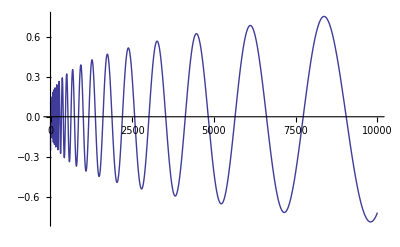

```mathematica
Plot[Re@pla[n,.7+20I],{n,1,10000}]
```

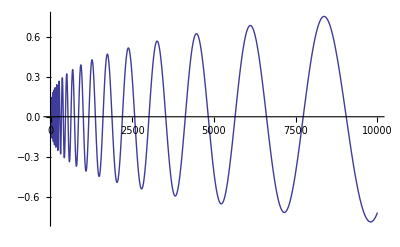

```mathematica
Plot[Re@plb[n,.7+20I],{n,1,10000}]
```

```mathematica
pb[n_,s_]:= n^s HarmonicNumber[n,s]/s-n^(1-s)HarmonicNumber[n,1-s]/(1-s)
```

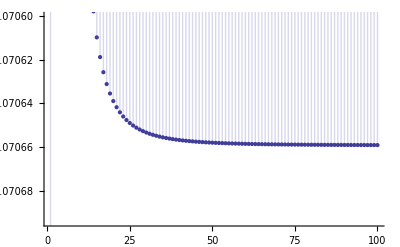

```mathematica
DiscretePlot[Im@pb[n,N@ZetaZero@1],{n,1,100}]
```

```mathematica
pb[1000,N@ZetaZero@1]
```

0.-0.0706593 ⅈ

```mathematica
N[n^s/s -Pi^(1/2-s) Gamma[s/2]/Gamma[(1-s)/2] n^(1-s)/(1-s)/.s->1/3]
```

3. n^(1/3)-3.77185 n^(2/3)

```mathematica
g1xa[n_,s_]:=n^s HarmonicNumber[n,s]/s-n^(1-s) HarmonicNumber[n,(1-s)]/(1-s)
g1xb[n_,s_]:=(n^s/s-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2]n^(1-s)/(1-s))Zeta[s]
```

```mathematica
{g1xa[n,s],g1xb[n,s]}/.n->1000000000/.s->N@ZetaZero@10
```

{0.-0.020089 ⅈ,-2.54438×10^-11-6.94188×10^-12 ⅈ}

```mathematica
1./(ZetaZero@1)
```

0.00249949-0.0706593 ⅈ

```mathematica
g1xa[1000000000,N@ZetaZero@1]
```

0.-0.0706591 ⅈ

```mathematica
g1xc[n_,s_]:=s n^(1-s) HarmonicNumber[n,(1-s)]-(1-s)n^s HarmonicNumber[n,s]
g1xc2[n_,s_]:=s n^(1-s) (Zeta[1-s]-Zeta[1-s,n+1])-(1-s)n^s( Zeta[s]-Zeta[s,n+1])
g1xc3[n_,s_]:=s n^(1-s) Zeta[1-s]-s n^(1-s) Zeta[1-s,n+1]-(1-s)n^s Zeta[s]+(1-s)n^s Zeta[s,n+1]
g1xc3a[n_,s_]:={s n^(1-s) Zeta[1-s],-s n^(1-s) Zeta[1-s,n+1],-(1-s)n^s Zeta[s],(1-s)n^s Zeta[s,n+1]}
g1xc3a2[n_,s_]:={s n^(1-s) HarmonicNumber[n,(1-s)],-(1-s)n^s HarmonicNumber[n,s]}
g1xc3c[n_,s_]:={n^(1-s) Zeta[1-s]/(1-s),-n^(1-s) Zeta[1-s,n+1]/(1-s),-n^s Zeta[s]/s,n^s Zeta[s,n+1]/s}
g1xc3c2[n_,s_]:={n^(1-s) HarmonicNumber[n,(1-s)]/(1-s),-n^s HarmonicNumber[n,s]/s}
g1xd[n_,s_]:=Sum[s (n/j)^(1-s)-(1-s)(n/j)^s,{j,1,n}]
```

```mathematica
N@g1xd[50,ZetaZero@1+1I]
```

9.59233×10^-14-101.975 ⅈ

```mathematica
(N@ZetaZero@1+2I)/2
```

0.25+8.06736 ⅈ

```mathematica
N@ZetaZero[1]
```

0.5+14.1347 ⅈ

```mathematica
FullSimplify[((b[s]h[s]-b[1-s]h[1-s])(b[1-s]h[1-s]-b[s]h[s]))^(1/2)]
```

√(-(b[1-s] h[1-s]-b[s] h[s])^2)

```mathematica
FullSimplify[Expand[(b[s]-a[1-s]/a[s] b[1-s])(b[1-s]-a[s]/a[1-s]b[s])]]
```

-(a[1-s] b[1-s]-a[s] b[s])^2/(a[1-s] a[s])

```mathematica
ap[s_]:=2 Pi^(s/2)/Gamma[s/2]
bt[n_,s_]:=n^s/s
zt[n_,s_]:=(bt[n,s]HarmonicNumber[n,s]-bt[n,1-s]HarmonicNumber[n,1-s])/(bt[n,s]-ap[1-s]/ap[s]bt[n,1-s])
zm[s_]:=(Zeta[s]Zeta[1-s])^(1/2)
```

```mathematica
zt[100000,.5+I]
```

0.143215-0.718479 ⅈ

```mathematica
Zeta[.5+I]
```

0.143936-0.7221 ⅈ

```mathematica
zt[n,s]
```

(-(n^(1-s) HarmonicNumber[n,1-s])/(1-s)+(n^s HarmonicNumber[n,s])/s)/(n^s/s-(n^(1-s) π^((1-s)/2-s/2) Gamma[s/2])/((1-s) Gamma[(1-s)/2]))

```mathematica
FullSimplify@Expand[zt[n,s]zt[n,1-s]]
```

(π^(1/2+s) Gamma[1/2-s/2] Gamma[s/2] (n s HarmonicNumber[n,1-s]+n^(2 s) (-1+s) HarmonicNumber[n,s])^2)/((-2 n^(2 s) π^s Gamma[3/2-s/2]+n √π s Gamma[s/2])^2)

```mathematica
((π^(1/2+s) Gamma[1/2-s/2] Gamma[s/2])^(1/2) (n s HarmonicNumber[n,1-s]+n^(2 s) (-1+s) HarmonicNumber[n,s]))/(-2 n^(2 s) π^s Gamma[3/2-s/2]+n √π s Gamma[s/2])
```

(√(π^(1/2+s) Gamma[1/2-s/2] Gamma[s/2]) (n s HarmonicNumber[n,1-s]+n^(2 s) (-1+s) HarmonicNumber[n,s]))/(-2 n^(2 s) π^s Gamma[3/2-s/2]+n √π s Gamma[s/2])

```mathematica
zsq[n_,s_]:=((π^(1/2+s) Gamma[1/2-s/2] Gamma[s/2])^(1/2) (n s HarmonicNumber[n,1-s]+n^(2 s) (-1+s) HarmonicNumber[n,s]))/(-2 n^(2 s) π^s Gamma[3/2-s/2]+n √π s Gamma[s/2])
zsq2[n_,s_]:=((π^(1/2+s) )^(1/2)(Gamma[1/2-s/2] Gamma[s/2])^(1/2) (s n^-s HarmonicNumber[n,1-s]+n^(s-1) (-1+s) HarmonicNumber[n,s]))/(-2 n^(s-1) Pi^s Gamma[3/2-s/2]+ Pi^(1/2) s n^-s Gamma[s/2])
zsq3[n_,s_]:=((-π^(1/4+s/2) )(Gamma[1/2-s/2] Gamma[s/2])^(1/2) (s n^-s HarmonicNumber[n,1-s]+n^(s-1) (-1+s) HarmonicNumber[n,s]))/(-2 n^(s-1) Pi^s Gamma[1+(1-s)/2]+ Pi^(1/2) s n^-s Gamma[s/2])
zsq4[n_,s_]:=((Gamma[1/2-s/2] Gamma[s/2])^(1/2) ( n^(-s)HarmonicNumber[n,1-s]/(1-s)-n^(s-1)  HarmonicNumber[n,s]/s))/(2/(1-s) n^(s-1)π^(-1/4+s/2) Gamma[1+(1-s)/2]/s- π^(1/4-s/2) n^-s  Gamma[s/2]/(1-s))
zsq5[n_,s_]:=(n^(1-s)HarmonicNumber[n,1-s]/(1-s)-n^s  HarmonicNumber[n,s]/s)/(n^s/s  π^(-1/4+s/2)(Gamma[(1-s)/2]/ Gamma[s/2])^(1/2)- π^(1/4-s/2) n^(1-s)/(1-s)  (Gamma[s/2]/Gamma[1/2-s/2])^(1/2))
zsq6[n_,s_]:=(n^(1-s)HarmonicNumber[n,1-s]/(1-s)-n^s  HarmonicNumber[n,s]/s)/(n^s/s  π^(-1/4+s/2)(Gamma[(1-s)/2]/ Gamma[s/2])^(1/2)- π^(1/4-s/2) n^(1-s)/(1-s)  (Gamma[s/2]/Gamma[(1-s)/2])^(1/2))
```

```mathematica
Chop@zsq6[10000000,N@ZetaZero@1+.1]
```

0.000713535+0.0793222 ⅈ

```mathematica
N@zm[ZetaZero@1-.1]
```

0.000651963-0.0793368 ⅈ

```mathematica
Abs[Zeta[.4+I]]
```

0.663341

```mathematica
Expand[(π^(1/2+s) )^(1/2)]
```

√(π^(1/2+s))

```mathematica
(3^(1/2+s))^(1/2)/.s->3.2
```

7.63263

```mathematica
(3^(1/4+s/2))/.s->3.2
```

7.63263

```mathematica
FullSimplify[Pi^s /(-π^(1/4+s/2) )]
```

-π^(-1/4+s/2)

```mathematica
FullSimplify[Pi^(1/2)/(-π^(1/4+s/2) )]
```

-π^(1/4-s/2)

```mathematica
s(1-s)/.s->N@ZetaZero@1
```

200.04+0. ⅈ

```mathematica
N@ZetaZero@1 / (1/N@ZetaZero@1)
```

-199.54+14.1347 ⅈ

```mathematica
ffo[n_,s_]:=(1-s) n^s HarmonicNumber[n,s]-s n^(1-s)HarmonicNumber[n,1-s]
ffp[n_,s_]:=n^s/s HarmonicNumber[n,s]-n^(1-s)/(1-s)HarmonicNumber[n,1-s]
ffq[n_,s_]:=((1-s) n^s HarmonicNumber[n,s]-s n^(1-s)HarmonicNumber[n,1-s])/(s(1-s))^(1/2)
ffr[n_,s_]:=(s /(1-s))^(1/2) n^(1-s)HarmonicNumber[n,1-s]-((1-s) /s)^(1/2)n^s HarmonicNumber[n,s]
```

```mathematica
ffo[100000,N@ZetaZero@2]/ffp[100000,N@ZetaZero@2]
```

442.176+0. ⅈ

```mathematica
N@ffr[10000000,ZetaZero@1]
```

1.16415×10^-10+0.999375 ⅈ

```mathematica
(s-s^2)^(1/2)
```

√(s-s^2)

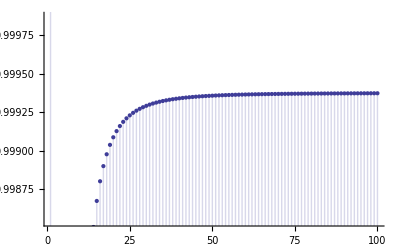

```mathematica
DiscretePlot[ Im[ ffr[n,ZetaZero@1]],{n,1,100}]
```

```mathematica
i1a[n_,s_]:=(n^s HarmonicNumber[n,s]/s-n^(1-s) HarmonicNumber[n,(1-s)]/(1-s))/(n^s/s-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2]n^(1-s)/(1-s))
i1b[n_,s_]:=((1-s)n^s HarmonicNumber[n,s]-s n^(1-s) HarmonicNumber[n,(1-s)])/(n^s (1-s)-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2]n^(1-s) s)
i1b2[n_,s_]:=Zeta[s]
i1c[n_,s_]:=(1-s)n^s HarmonicNumber[n,s]-s n^(1-s) HarmonicNumber[n,(1-s)]
i1c2[n_,s_]:=Zeta[s](n^s (1-s)-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2]n^(1-s) s)
i1c3o[n_,s_]:=(1-s)n^s (Zeta[s]-Zeta[s,n+1])-s n^(1-s) (Zeta[1-s]-Zeta[1-s,n+1])
i1c3[n_,s_]:=(1-s)n^s (-Zeta[s,n+1])-s n^(1-s) (-Zeta[1-s,n+1])
```

```mathematica
{i1c[10000000000,N@ZetaZero@1+.00000001I],i1c2[10000000000,N@ZetaZero@1+.00000001I],i1c3[10000000000,N@ZetaZero@1+.00000001I]}
```

{0.-14.1542 ⅈ,-7.1839×10^-9-0.019663 ⅈ,0.-14.1346 ⅈ}

```mathematica
{i1b[10000000000,N@ZetaZero@1+.00000001I],i1b2[10000000000,N@ZetaZero@1+.00000001I]}
```

{-8.97638×10^-7+5.63847×10^-6 ⅈ,-1.247×10^-9+7.83297×10^-9 ⅈ}

```mathematica
Expand[(((1-s)^(1/2)/s^(1/2)))/(1-s)]
```

1/(√(1-s) √s)

```mathematica
N[1/(√(1-s) √s)/.s->N@ZetaZero@1]
```

0.0707035+0. ⅈ

```mathematica
pa[n_,s_]:= (1-s)n^s HarmonicNumber[n,s]
pax[n_,s_]:= (1-s)n^(s-1) HarmonicNumber[n,s]
pa2[n_,s_]:= n^s/s HarmonicNumber[n,s]
pa3[n_,s_]:= ((1-s)/s)^(1/2)n^s HarmonicNumber[n,s]
pa4[n_,s_]:= (s/(1-s))^(1/2)n^s HarmonicNumber[n,s]
pa5[n_,a_,s_]:= ((1-s)^a s^-(1-a))n^s HarmonicNumber[n,s]
```

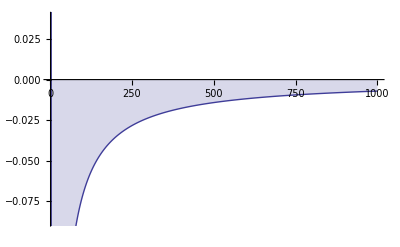

```mathematica
DiscretePlot[Im[pax[n,N@ZetaZero@1]],{n,1,1000}]
```

```mathematica
pa[10000000,N@ZetaZero@1]+N@ZetaZero@1/2 - 1/2-10000000
```

-1.67079×10^-6-3.39502×10^-7 ⅈ

```mathematica
(N@ZetaZero@1)
```

0.5+14.1347 ⅈ

```mathematica
pa[100,N@ZetaZero@1]
```

100.083-7.06735 ⅈ

```mathematica
pa5[1000,.5,N@ZetaZero@4]
```

32.8691-0.499932 ⅈ

```mathematica
(1000 (1/((1-N@ZetaZero@4) N@ZetaZero@4))^(1/2))
```

32.8634+0. ⅈ

```mathematica
pa3[100000,N@ZetaZero@1]
```

7070.37-0.499687 ⅈ

```mathematica
pa5[100000,.5,N@ZetaZero@1]
```

7070.37-0.499687 ⅈ

```mathematica
((ZetaZero@1)(1-ZetaZero@1))^(-1/2)(100000+ 1/2-N@ZetaZero@1/2)
```

7070.37-0.499687 ⅈ

```mathematica
Chop[pa5[100000,.5,N@ZetaZero@1]/pa5[100000,1,N@ZetaZero@1]]
```

0.0707035

```mathematica
N[ZetaZero@1^(1/2)(1-ZetaZero@1)^(-1/2)]
```

0.0353518+0.999375 ⅈ

```mathematica
0.07070352773181221pa5[100000,1,N@ZetaZero@1]
```

7070.37-0.499687 ⅈ

```mathematica
pa5[100000,.5,N@ZetaZero@1]
```

7070.37-0.499687 ⅈ

```mathematica
1/(N@ZetaZero@1-1/2)
```

0.-0.0707477 ⅈ

```mathematica
N[(s-s^2)^(-1/2)(s/2)/.s->.5+14.14I]
```

0.0176693+0.499688 ⅈ

```mathematica
(s-s^2)^(-1/2)(s/2)
```

s/(2 √(s-s^2))

```mathematica
N[(4s-4s^2)^(-1/2)s/.s->.5+14.14I]
```

0.0176693+0.499688 ⅈ

```mathematica
N[((1-s)/s)^(-1/2)/2/.s->.5+14.14I]
```

0.0176693+0.499688 ⅈ

```mathematica
(* so this thing has an abs of exactly 1/2 when re(s) is 1/2 *)
```

1/(2 √(-1+1/s))

```mathematica
FullSimplify[(s(1-s))^(-1/2)(1/2-s/2)]
```

(√(1-s))/(2 √s)

```mathematica
1/2(s(1-s))^(-1/2)
```

1/(2 √((1-s) s))

```mathematica
FullSimplify[1/2(s(1-s))^(-1/2)-1/2((1-s)/s)^(-1/2)]
```

1/2 (-1/(√(-1+1/s))+1/(√(-(-1+s) s)))

```mathematica
(√(1-s))/(2 √s)/.s->.5+2I
```

0.121268-0.485071 ⅈ

```mathematica
(s(1-s))^(-1/2)(1/2-s/2)/.s->.5+2I
```

0.121268-0.485071 ⅈ

```mathematica
1/2((1-s)/s)^(-1/2)/.s->.5+2I
```

0.121268+0.485071 ⅈ

```mathematica
n(s(1-s))^(-1/2)+1/2(s/(1-s))^(1/2)/.s->N@ZetaZero@1/.n->100000
```

7070.37+0.499687 ⅈ

```mathematica
pa3[100000,N@ZetaZero@1]
```

7070.37-0.499687 ⅈ

```mathematica
Chop[pa5[100000,0,N@ZetaZero@1]/pa5[100000,1,N@ZetaZero@1]]
```

0.00499899

```mathematica
1/(s(1-s))/.s->N@ZetaZero@1
```

0.00499899+0. ⅈ

```mathematica
pa5[100000,0,N@ZetaZero@1]
```

499.9-0.0353297 ⅈ

```mathematica
(n+(1-s)/2)/s/(1-s) /.s->N@ZetaZero@1/.n->100000
```

499.9-0.0353297 ⅈ

```mathematica
FullSimplify[((1-s)/2)/s/(1-s)]
```

1/(2 s)

```mathematica
(n)/s/(1-s)
```

n/((1-s) s)

```mathematica
n (s(1-s))^(-1/2)/.s->.5+5I/.n->100000
```

19900.7+0. ⅈ

```mathematica
(s/(1-s))^(1/2)/2/.s->.5+14.14I
```

0.0176693+0.499688 ⅈ

```mathematica
n(s(1-s))^(-1/2)+1/2(s/(1-s))^(1/2)/.s->N@ZetaZero@1/.n->100
```

7.08803+0.499687 ⅈ

```mathematica
pa3[100,N@ZetaZero@1]
```

7.07624-0.499686 ⅈ

```mathematica
pa6[n_,s_]:= (1-s)n^s HarmonicNumber[n,s]
```

```mathematica
pa6[10000000,N@ZetaZero@1]-pa6[10000000,1-N@ZetaZero@1]
```

0.-14.1347 ⅈ

```mathematica
n^(1-s)/(1-s)+n^-s/2-n^(-s-1)s /12+n^(-s-3)s(s+1)(s+2)/720
```

n^-s/2+n^(1-s)/(1-s)-1/12 n^(-1-s) s+1/720 n^(-3-s) s (1+s) (2+s)

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
bern[k_]:=If[k==1,1/2,BernoulliB[k]]
bs[n_,s_,t_]:=Sum[FullSimplify[ bin[1-s,k]/(1-s)bern[k] n^(1-s-k)],{k,0,t}]
```

```mathematica
bs[n,s,10]
```

n^-s/2+n^(1-s)/(1-s)-1/12 n^(-1-s) s+1/720 n^(-3-s) s (1+s) (2+s)-(n^(-5-s) s (1+s) (2+s) (3+s) (4+s))/30240+(n^(-7-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s))/1209600-(n^(-9-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s))/47900160

```mathematica
bs[n,s,20]
```

n^-s/2+n^(1-s)/(1-s)-1/12 n^(-1-s) s+1/720 n^(-3-s) s (1+s) (2+s)-(n^(-5-s) s (1+s) (2+s) (3+s) (4+s))/30240+(n^(-7-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s))/1209600-(n^(-9-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s))/47900160+(691 n^(-11-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s))/1307674368000-(n^(-13-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s))/74724249600+(3617 n^(-15-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s) (13+s) (14+s))/10670622842880000-(43867 n^(-17-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s) (13+s) (14+s) (15+s) (16+s))/5109094217170944000+(174611 n^(-19-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s) (13+s) (14+s) (15+s) (16+s) (17+s) (18+s))/802857662698291200000

```mathematica
FullSimplify@Expand[bs[n,s,10]/bs[n,1-s,10]]
```

-(n^(1-2 s) s (239500800 n^10-119750400 n^9 (-1+s)+19958400 n^8 (-1+s) s-332640 n^6 (-1+s) s (1+s) (2+s)+7920 n^4 (-1+s) s (1+s) (2+s) (3+s) (4+s)-198 n^2 (-1+s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s)+5 (-1+s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s)))/((-1+s) (239500800 n^10+119750400 n^9 s+19958400 n^8 (-1+s) s-332640 n^6 (-3+s) (-2+s) (-1+s) s+7920 n^4 (-5+s) (-4+s) (-3+s) (-2+s) (-1+s) s-198 n^2 (-7+s) (-6+s) (-5+s) (-4+s) (-3+s) (-2+s) (-1+s) s+5 (-9+s) (-8+s) (-7+s) (-6+s) (-5+s) (-4+s) (-3+s) (-2+s) (-1+s) s))

```mathematica
HarmonicNumber[n,s]/bs[n,s,10]-HarmonicNumber[n,1-s]/bs[n,1-s,10]/.s->.95+3I/.n->1000000000000000
```

0.0692592+0.327965 ⅈ

```mathematica
Expand[Sum[j^2,{j,1,n}]]
```

n/6+n^2/2+n^3/3

```mathematica
bs[100,N@ZetaZero@2,10]
```

0.208036-0.429927 ⅈ

```mathematica
fno[n_,s_]:=1/(n^-s/2+n^(1-s)/(1-s)-1/12 n^(-1-s) s+1/720 n^(-3-s) s (1+s) (2+s))
fno2[n_,s_]:=1/(n^-s/2+n^(1-s)/(1-s)-1/12 n^(-1-s) s+1/720 n^(-3-s) s (1+s) (2+s)-(n^(-5-s) s (1+s) (2+s) (3+s) (4+s))/30240+(n^(-7-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s))/1209600-(n^(-9-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s))/47900160)
fn[n_,s_]:=1/(n^-s/2+n^(1-s)/(1-s)-1/12 n^(-1-s) s+1/720 n^(-3-s) s (1+s) (2+s)-(n^(-5-s) s (1+s) (2+s) (3+s) (4+s))/30240+(n^(-7-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s))/1209600-(n^(-9-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s))/47900160+(691 n^(-11-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s))/1307674368000-(n^(-13-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s))/74724249600+(3617 n^(-15-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s) (13+s) (14+s))/10670622842880000-(43867 n^(-17-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s) (13+s) (14+s) (15+s) (16+s))/5109094217170944000+(174611 n^(-19-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s) (13+s) (14+s) (15+s) (16+s) (17+s) (18+s))/802857662698291200000)
pm[n_,s_]:= (fn[n,s]HarmonicNumber[n,s]-fn[n,1-s]HarmonicNumber[n,1-s])/(fn[n,s]-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] fn[n,1-s])
pmx[n_,s_]:= (1-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] fn[n,1-s]/fn[n,s])^-1 HarmonicNumber[n,s]-(fn[n,s]/fn[n,1-s]-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] )^-1HarmonicNumber[n,1-s]
pmo[n_,s_]:= (fn[n,s]HarmonicNumber[n,s]-fn[n,1-s]HarmonicNumber[n,1-s])
fn2[n_,s_]:= (1-s)n^s
pm2[n_,s_]:= (fn2[n,s]HarmonicNumber[n,s]-fn2[n,1-s]HarmonicNumber[n,1-s])/(fn2[n,s]-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] fn2[n,1-s])
pmo2[n_,s_]:= (fn2[n,s]HarmonicNumber[n,s]-fn2[n,1-s]HarmonicNumber[n,1-s])
```

```mathematica
pmx[10,.7+3I]
```

0.571252-0.0923229 ⅈ

```mathematica
Zeta[.7+3I]
```

0.571252-0.0923229 ⅈ

```mathematica
pm[10000,s]-Zeta[s]/.s->N@ZetaZero@10000+.5I
```

-3.76419×10^-11+3.47209×10^-11 ⅈ

```mathematica
pm[4,s]/.s->.7
```

-2.77839

```mathematica
Zeta[.7]
```

-2.77839

```mathematica
HarmonicNumber[4,s]/.s->.5
```

2.78446

```mathematica
pmo[1000,N@ZetaZero@100+.1I]
```

0.-0.666732 ⅈ

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
bern[k_]:=If[k==1,1/2,BernoulliB[k]]
bs[n_,s_,t_]:=1/(1-s)Sum[FullSimplify[ bin[1-s,k]bern[k] n^(1-s-k)],{k,0,t}]
```

```mathematica
fna[n_,s_]:=(1-s)n^s
pma[n_,s_]:= (fna[n,s]HarmonicNumber[n,s]-fna[n,1-s]HarmonicNumber[n,1-s])/(fna[n,s]-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] fna[n,1-s])
pma2[n_,s_]:= {fna[n,s]HarmonicNumber[n,s],-fna[n,1-s]HarmonicNumber[n,1-s],fna[n,s],-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] fna[n,1-s]}
pmx[n_,s_]:= (1-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] fna[n,1-s]/fn[n,s])^-1 HarmonicNumber[n,s]-(fna[n,s]/fn[n,1-s]-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] )^-1HarmonicNumber[n,1-s]
pmx2[n_,s_]:= {(1-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] fna[n,1-s]/fn[n,s])^-1, HarmonicNumber[n,s],-(fna[n,s]/fn[n,1-s]-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] )^-1,HarmonicNumber[n,1-s]}
```

```mathematica
Chop@pma2[70000000000,N@ZetaZero@1]
```

{7.×10^10-7.06501 ⅈ,-7.×10^10-7.06501 ⅈ,3.40939×10^6-1.54236×10^6 ⅈ,3.71979×10^6+407400. ⅈ}

```mathematica
pma[700,N@ZetaZero@1]
```

0.0451776-0.283781 ⅈ

```mathematica
Zeta[.7]
```

-2.77839

```mathematica
fn[n_,s_]:=1/(n^-s/2+n^(1-s)/(1-s)-1/12 n^(-1-s) s+1/720 n^(-3-s) s (1+s) (2+s)-(n^(-5-s) s (1+s) (2+s) (3+s) (4+s))/30240+(n^(-7-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s))/1209600-(n^(-9-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s))/47900160+(691 n^(-11-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s))/1307674368000-(n^(-13-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s))/74724249600+(3617 n^(-15-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s) (13+s) (14+s))/10670622842880000-(43867 n^(-17-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s) (13+s) (14+s) (15+s) (16+s))/5109094217170944000+(174611 n^(-19-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s) (13+s) (14+s) (15+s) (16+s) (17+s) (18+s))/802857662698291200000)
pmxo[n_,s_]:= (fn[n,s]HarmonicNumber[n,s]-fn[n,1-s]HarmonicNumber[n,1-s])/(fn[n,s]-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] fn[n,1-s])
pmxa[n_,s_]:= (1-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] fn[n,1-s]/fn[n,s])^-1 HarmonicNumber[n,s]-(fn[n,s]/fn[n,1-s]-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] )^-1HarmonicNumber[n,1-s]
pmxa2[n_,s_]:= (1-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] fn[n,1-s]/fn[n,s])^-1 (Zeta[s]-Zeta[s,n+1])-(fn[n,s]/fn[n,1-s]-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] )^-1(Zeta[1-s]-Zeta[1-s,n+1])
pmxa3[n_,s_]:= {(1-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] fn[n,1-s]/fn[n,s])^-1 (Zeta[s]),-
(1-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] fn[n,1-s]/fn[n,s])^-1 (Zeta[s,n+1]),-
(fn[n,s]/fn[n,1-s]-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] )^-1(Zeta[1-s]),+
(fn[n,s]/fn[n,1-s]-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] )^-1(Zeta[1-s,n+1])}
pmxa4[n_,s_]:= (1-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] fn[n,1-s]/fn[n,s])^-1 (Zeta[s])-(fn[n,s]/fn[n,1-s]-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] )^-1(Zeta[1-s])
pmxa4a[n_,s_]:= {(1-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] fn[n,1-s]/fn[n,s])^-1, (Zeta[s]),-(fn[n,s]/fn[n,1-s]-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] )^-1,(Zeta[1-s])}
```

```mathematica
pmxa3[5,.7]
```

{-4.51131,9.02863,1.73292,-9.02863}

```mathematica
Zeta[.9]
```

-9.43011

```mathematica
pmxa4[I,.9]
```

-9.43011+5.86198×10^-14 ⅈ

```mathematica
pmxa4a[I,.9]
```

{0.129863-0.892596 ⅈ,-9.43011,13.6069+13.9581 ⅈ,-0.603038}

```mathematica
FullSimplify[((a[s]-b[s])^-1)/((1-b[s]/a[s])^-1-1)]
```

1/b[s]

```mathematica
pmxr[n_,s_]:= (1-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] fn[n,1-s]/fn[n,s])^-1 (Zeta[s]-Zeta[s,n+1])-(fn[n,s]/fn[n,1-s]-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] )^-1(Zeta[1-s]-Zeta[1-s,n+1])
pmxa4[n_,s_]:= (1-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] fn[n,1-s]/fn[n,s])^-1 (Zeta[s])-(fn[n,s]/fn[n,1-s]-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] )^-1(Zeta[1-s])
pmxa4s[n_,s_]:= (1-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2])^-1 (Zeta[s])-(1-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] )^-1(Zeta[1-s])
pmxa5[n_,s_]:= -(1-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] fn[n,1-s]/fn[n,s])^-1 (Zeta[s,n+1])+(fn[n,s]/fn[n,1-s]-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] )^-1(Zeta[1-s,n+1])
pmxa5a[n_,s_]:= {-(1-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] fn[n,1-s]/fn[n,s])^-1 (Zeta[s,n+1]),(fn[n,s]/fn[n,1-s]-Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2] )^-1(Zeta[1-s,n+1])}
dis[n_,s_]:=HarmonicNumber[n,s]-1/fn[n,s]
```

```mathematica
pmxa5a[60,-1.0]
```

{-0.000837346,0.000837346}

```mathematica
Zeta[.3+12I]
```

1.04409-0.857521 ⅈ

```mathematica
pmxr[10,.3+12I]
```

1.04409-0.857521 ⅈ

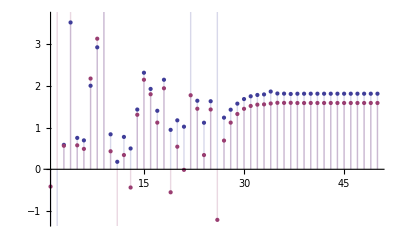

```mathematica
DiscretePlot[{Re@pmxr[n,.6+190I],Im@pmxr[n,.6+190I]},{n,1,50}]
```

```mathematica
DiscretePlot[{Re@pmxr[n,.6+190I],Im@pmxr[n,.6+190I]},{n,1,50}]
```

-Graphics-